## Load package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["diffTVR`"]
```

```mathematica
?diffTVR`*
```

# Absolute value, white noise

## Data

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
styleExactF=Darker[Green];
styleExact=Opacity[0.4,Darker[Green]];
styleNoisy=Directive[Opacity[0.7],colors[[1]]];
styleFiltered1=colors[[2]];
styleFiltered2=Darker[Magenta];
styleAve=Brown;
styleTVR=Black;
styleTVRFiltered=Gray;
styleFiltered1Filtered=Lighter[styleFiltered1];
styleFiltered2Filtered=Lighter[styleFiltered2];
styleNoisyFiltered=Blue;
```

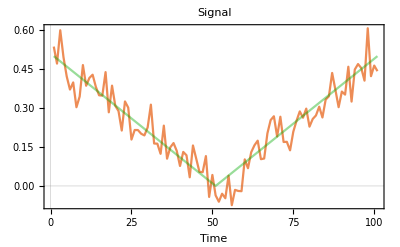
-Graphics- |

```mathematica
dx=0.01;
dataExact=Table[Abs[x-0.5],{x,0,1,dx}];
dataNoisy=Table[x+RandomVariate[NormalDistribution[0,0.05]],{x,dataExact}];
leg=LineLegend[{styleExact,styleNoisy},{"Exact signal","Noisy signal"}];
pltData=Grid[{{ListLinePlot[{dataNoisy,dataExact},PlotStyle->{styleNoisy,styleExact},FrameLabel->{"Time"},PlotLabel->"Signal"],leg}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["example_abs_figures/signal.png",pltData,ImageResolution->200]
```

example_abs_figures/signal.png

```mathematica
diff[x_]:=(RotateLeft[x]-x)[[;;-2]]/(dx)
```

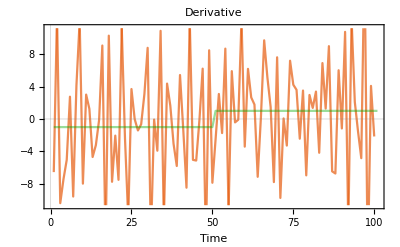

```mathematica
derivExact=Table[If[x<0.5,-1,1],{x,0,1,dx}];
derivNoisy=diff[dataNoisy];
pltDeriv=ListLinePlot[{derivNoisy,derivExact},PlotStyle->{styleNoisy,styleExact},PlotLabel->"Derivative",FrameLabel->{"Time"}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["example_abs_figures/deriv.png",pltDeriv,ImageResolution->200]
```

example_abs_figures/deriv.png

## Diff TVR

```mathematica
derivGuess=ConstantArray[0,Length[dataNoisy]+1];
noOptSteps=100;
alpha=0.2;
derivFinal=getDiffTVR[dataNoisy,derivGuess,noOptSteps,dx,alpha];
```

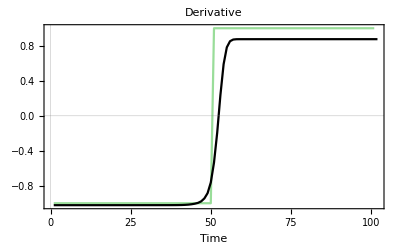
-Graphics- |

```mathematica
leg=LineLegend[{styleExact,styleTVR},{"Exact","TVR"}];
pTVR=Grid[{{ListLinePlot[{derivExact,derivFinal},PlotStyle->{styleExact,styleTVR},PlotLabel->"Derivative",FrameLabel->{"Time"}],leg}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["example_abs_figures/tvr.png",pTVR,ImageResolution->200]
```

example_abs_figures/tvr.png